```mathematica
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/CoolTools2.m"]
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/usefulFunctions.wl"]
```

SetDelayed::write: Tag BlockDiagonalMatrix in BlockDiagonalMatrix[b:{__?MatrixQ}] is Protected.

```mathematica
rzs = {0, 0.5, 0.8};
targets = (IdentityMatrix[2] + # PauliMatrix[3])/2 & /@ rzs;
```

```mathematica
(*estado inicial*)
initState = initStateGenerator[1000, 0.001, 0.3, targets[[2]], 0.002];
```

```mathematica
1000^(-0.867)
```

0.00250611

## La preimagen “mala”

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/muestras_MH/distintasN_betasydeltas_Rp5_Pp3/samples"];
sampleRp5Pp3 = Get["MHsample_N=40000_delta=0.05_beta=1000_rz=0.5_p=0.3.wl"];
```

```mathematica
Clear[sampleRp5Pp3]
```

## La preimagen “buena”

```mathematica
metropolisHastingsSampleRIGHT[size_,β_,δ_,swapP_,initialstate_,targetstate_]:= Module[{n = 0, X = initialstate, Y, U, α, statelist = {}, acceptances = 0},
	While[n < size,
		U = randomSmallEvolution[4,δ];
		Y = U . X . ConjugateTranspose[U];
		α = Min[testDistribution[β,targetstate,Y,swapP]/testDistribution[β,targetstate,X,swapP],1];
		X = RandomChoice[{α, 1 - α}->{Y,X}];
		If[X == Y, acceptances++];
		AppendTo[statelist, X];
		n++
	];
	Return[{statelist, acceptances/size}]];
```

```mathematica
rightSampleRp5Pp3 = Timing[metropolisHastingsSampleRIGHT[100000, 1000, 0.001, 0.3, initState, targets[[2]]]];
```

```mathematica
Clear[rightSampleRp5Pp3]
```

```mathematica
rightSampleRp5Pp3[[2,2]]//N (*acceptance rate*)
```

0.001438

## Comparando la “mala” y la “buena”

```mathematica
(*fidelidad entre edos promedio*)
{fidelity[ρaverageTwoQubitsbasiscomp[0.3, 0.5], preimageMean[sampleRp5Pp3[[2]]]], 
fidelity[ρaverageTwoQubitsbasiscomp[0.3, 0.5], preimageMean[rightSampleRp5Pp3[[2,1]]]]}
```

Part::partd: Part specification sampleRp5Pp3⟦2⟧ is longer than depth of object.

{fidelity[{{0.474206,0.,0.,0.},{0.,0.0535714,-0.0853175,0.},{0.,-0.0853175,0.371032,0.},{0.,0.,0.,0.10119}},preimageMean[sampleRp5Pp3⟦2⟧]],0.770216}

Part::partd: Part specification sampleRp5Pp3⟦2⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through 500 in sampleRp5Pp3⟦2⟧.

Part::pkspec1: The expression √(Abs[-0.75+coarseGraining2[1;;500,0.3]]^2+Abs[-0.25+coarseGraining2[1;;500,0.3]]^2+2 Abs[0.+coarseGraining2[Span[«2»],0.3]]^2) cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: √(Abs[-0.75+coarseGraining2[Part[«2»],0.3]]^2+Abs[-0.25+coarseGraining2[Part[«2»],0.3]]^2+2. Abs[0.+coarseGraining2[«2»]]^2)⟦√(Abs[-0.75+coarseGraining2[Span[«2»],0.3]]^2+Abs[-0.25+coarseGraining2[Span[«2»],0.3]]^2+2 Abs[0.+coarseGraining2[«2»]]^2)⟧ is not a list of numbers or pairs of numbers.

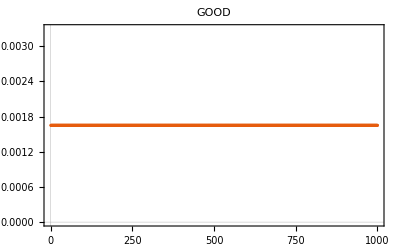
{ListPlot[√(Abs[-0.75+coarseGraining2[sampleRp5Pp3⟦2⟧,0.3]]^2+Abs[-0.25+coarseGraining2[sampleRp5Pp3⟦2⟧,0.3]]^2+2 Abs[0.+coarseGraining2[sampleRp5Pp3⟦2⟧,0.3]]^2)⟦√(Abs[-0.75+coarseGraining2[1;;500,0.3]]^2+Abs[-0.25+coarseGraining2[1;;500,0.3]]^2+2 Abs[0.+coarseGraining2[1;;500,0.3]]^2)⟧,PlotTheme→Scientific,PlotLabel→BAD],-Graphics-}

```mathematica
(*error*)
{ListPlot[distsToTarget[sampleRp5Pp3[[2]][[1;;500]], targets[[2]], 0.3], PlotTheme->"Scientific", PlotLabel->"BAD"],
ListPlot[distsToTarget[rightSampleRp5Pp3[[2,1]][[1;;1000]], targets[[2]], 0.3], PlotTheme->"Scientific", PlotLabel->"GOOD"]}
```

```mathematica
(*ergodicidad*)
brutalRefRp5Pp3 = ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.5.m"][[1;;100]]];
erg = ergodicityMeasure2[minDistancesVector[brutalRefRp5Pp3, sampleRp5Pp3[[2]]]];
```

```mathematica
ergRight = ergodicityMeasure2[minDistancesVector[brutalRefRp5Pp3, rightSampleRp5Pp3[[2,1]]]];
```

```mathematica
{erg, ergRight}
```

{0.393534,0.601109}

```mathematica
(*tiempo de ejecución*)
{sampleRp5Pp3[[1]]/60, rightSampleRp5Pp3[[1]]/60}
```

Part::partd: Part specification sampleRp5Pp3⟦1⟧ is longer than depth of object.

{sampleRp5Pp3⟦1⟧/60,1.03515}

```mathematica
visualizeBipartiteSystem[sampleRp5Pp3[[2]]]
```

```mathematica
visualizeBipartiteSystem[rightSampleRp5Pp3[[2,1]]]
```